Коэффициенты Фурье для функции f1

Piecewise[{{1/π, n==0}, {Sin[n]/(n π), True}}]

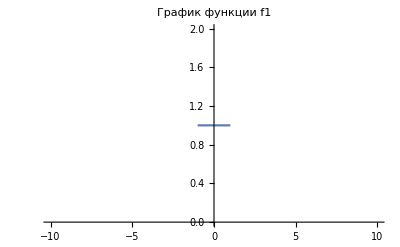

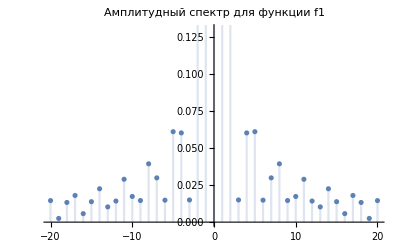

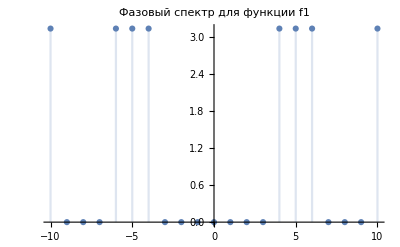

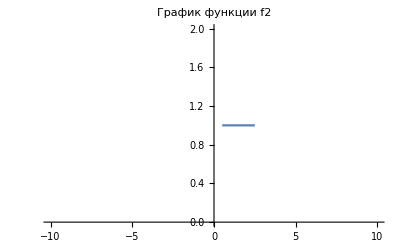

Коэффициенты Фурье для функции f2

Piecewise[{{0.31831, n==0}, {(0.31831 ⅇ^((0.-1.5 ⅈ) n) Sin[n])/n, True}}]

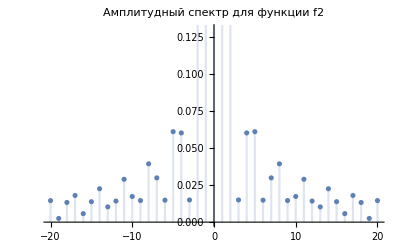

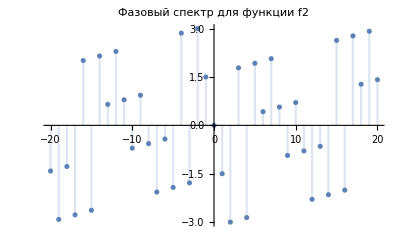

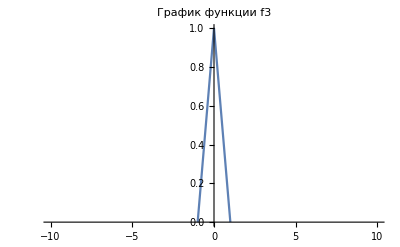

Коэффициенты Фурье для функции f3

Piecewise[{{1/(2 π), n==0}, {-(ⅇ^(-ⅈ n) (-1+ⅇ^(ⅈ n))^2)/(2 n^2 π), True}}]

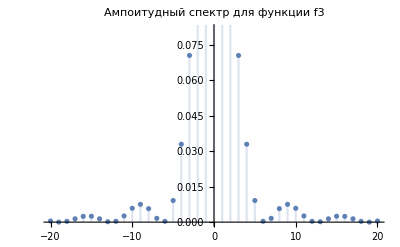

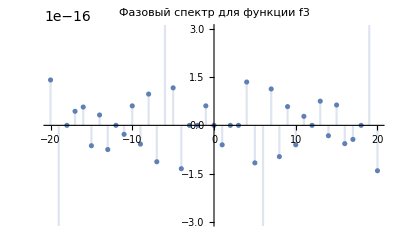

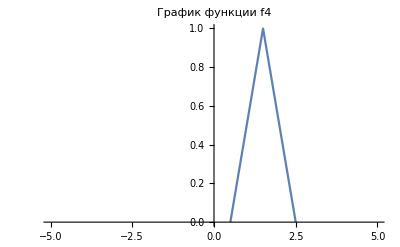

Коэффициенты Фурье для функции f4

Piecewise[{{0.159155, n==0}, {1/n^2((-0.159155-(0.+0.0795775 ⅈ) n) Cos[0.5 n]+(0.159155+(0.+0.238732 ⅈ) n) Cos[1.5 n]-0.0795775 n Sin[0.5 n]+(-0.159155 ⅇ^((0.-1. ⅈ) n) n+0.795775 ⅇ^((0.-2. ⅈ) n) n) Sin[0.5 n]+0.238732 n Sin[1.5 n]+(0.+0.31831 ⅈ) Cos[2. Abs[n]] Sign[n] Sin[0.5 Abs[n]]+0.31831 Sin[0.5 Abs[n]] Sin[2. Abs[n]]+1/Abs[n]^3(0.+0.238732 ⅈ) n^3 (Sign[n] (1. n Cos[1.5 Abs[n]]-1.66667 n Cos[2.5 Abs[n]]+0.666667 Sin[0.5 n]-0.666667 Sin[1.5 n])-(0.+1. ⅈ) n Sin[1.5 Abs[n]]+(0.+1.66667 ⅈ) n Sin[2.5 Abs[n]])), True}}]

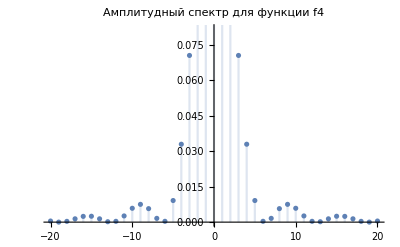

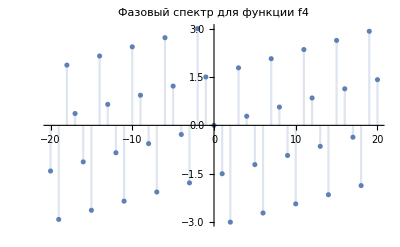

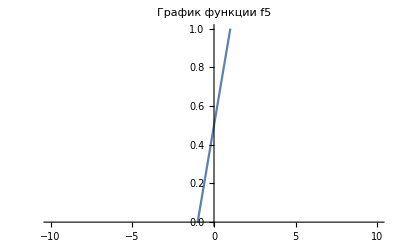

Коэффициенты Фурье для функции f5

Piecewise[{{1/(2 π), n==0}, {(ⅈ n Cos[n]+(-ⅈ+n) Sin[n])/(2 n^2 π), True}}]

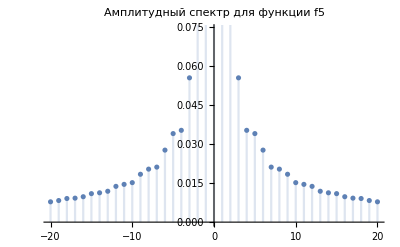

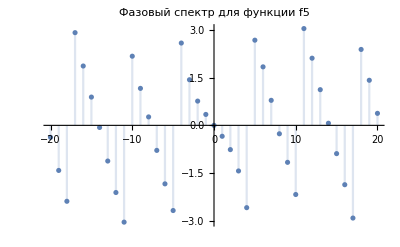

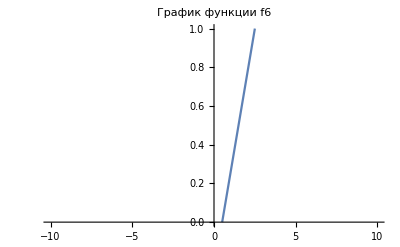

Коэффициенты Фурье для функции f6

Piecewise[{{0.159155, n==0}, {(ⅇ^((0.-1.5 ⅈ) n) ((0.+0.159155 ⅈ) n Cos[n]+((0.-0.159155 ⅈ)+0.159155 n) Sin[n]))/n^2, True}}]

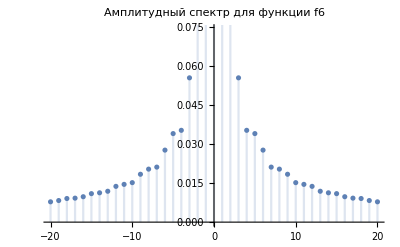

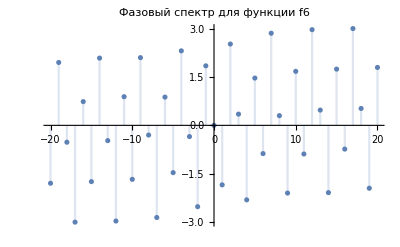

```mathematica
Clear[f1,f2,f3,f4,f5,f6,coeffs1,coeffs2,coeffs3,coeffs4,coeffs5,coeffs6]
f1[t_,τ_]:= Which[-τ≤ t≤τ , 1]
Text["Коэффициенты Фурье для функции f1"]
coeffs1[n_] = FourierCoefficient[f1[t,1],t,n]
Plot[f1[t,1],{t,-10,10},PlotLabel->"График функции f1"]
DiscretePlot[Abs[coeffs1[x]],{x,-20,20},PlotLabel->"Амплитудный спектр для функции f1"]
DiscretePlot[Arg[coeffs1[x]],{x,-10,10},PlotLabel->"Фазовый спектр для функции f1"]
f2[t_,τ_]:= Which[0+0.5≤ t≤2τ +0.5, 1]
Plot[f2[t,1],{t,-10,10},PlotLabel->"График функции f2"]
Text["Коэффициенты Фурье для функции f2"]
coeffs2[n_] = FourierCoefficient[f2[t,1],t,n]
DiscretePlot[Abs[coeffs2[x]],{x,-20,20},PlotLabel->"Амплитудный спектр для функции f2"]
DiscretePlot[Arg[coeffs2[x]],{x,-20,20},PlotLabel->"Фазовый спектр для функции f2"]
f3[t_,τ_] := Which[-τ≤ t≤τ ,-Abs[t]+τ ]
Plot[f3[t , 1] , {t , -10 , 10},PlotLabel->"График функции f3"]
Text["Коэффициенты Фурье для функции f3"]
coeffs3[n_] = FourierCoefficient[f3[t,1],t,n]
DiscretePlot[Abs[coeffs3[x]],{x,-20,20},PlotLabel->"Ампоитудный спектр для функции f3"]
DiscretePlot[Arg[coeffs3[x]],{x,-20,20},PlotLabel->"Фазовый спектр для функции f3"]
f4[t_,τ_] := Which[0.5≤ t≤2τ+0.5 ,-Abs[t-τ-0.5]+τ ]
Plot[f4[t,1],{t,-5,5},PlotLabel->"График функции f4"]
Text["Коэффициенты Фурье для функции f4"]
coeffs4[n_] = FourierCoefficient[f4[t,1],t,n]
DiscretePlot[Abs[coeffs4[x]],{x,-20,20},PlotLabel->"Амплитудный спектр для функции f4"]
DiscretePlot[Arg[coeffs4[x]],{x,-20,20},PlotLabel->"Фазовый спектр для функции f4"]
f5[t_,τ_] := Which[-τ≤ t≤τ ,(t+τ)/(2τ) ]
Plot[f5[t,1],{t,-10,10},PlotLabel->"График функции f5"]
Text["Коэффициенты Фурье для функции f5"]
coeffs5[n_] = FourierCoefficient[f5[t,1],t,n]
DiscretePlot[Abs[coeffs5[x]],{x,-20,20},PlotLabel->"Амплитудный спектр для функции f5"]
DiscretePlot[Arg[coeffs5[x]],{x,-20,20},PlotLabel->"Фазовый спектр для функции f5"]
f6[t_,τ_] := Which[0+0.5≤ t≤2τ+0.5 ,(t-0.5-τ)/(2τ)+0.5 ]
Plot[f6[t,1],{t , -10 , 10},PlotLabel->"График функции f6"]
Text["Коэффициенты Фурье для функции f6"]
coeffs6[n_] = FourierCoefficient[f6[t,1],t,n]
DiscretePlot[Abs[coeffs6[x]],{x,-20,20},PlotLabel->"Амплитудный спектр для функции f6"]
DiscretePlot[Arg[coeffs6[x]],{x,-20,20},PlotLabel->"Фазовый спектр для функции f6"]
```